# Neural Network Explorations

#### preliminaries

```mathematica
Manipulate[
Plot[PDF[NormalDistribution[0,sd],x],{x,-4,4},PlotRange->{0,1}],
{sd,1,4}]
```

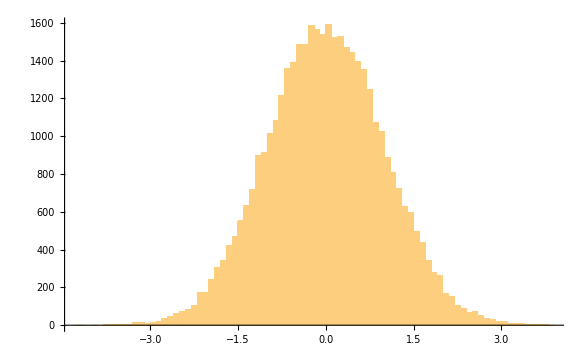

```mathematica
Histogram[RandomVariate[NormalDistribution[0,1],40000],60]
```

#### section 1

```mathematica
sample[center_,num_]:=RandomVariate[MultinormalDistribution[center,0.25IdentityMatrix[3]],num]
```

```mathematica
centers=RandomReal[{-6,6},{40,3}];
```

```mathematica
centers
```

{{5.87819,4.08369,-2.786},{1.50077,5.61334,-1.43875},{-3.22189,-1.12274,1.65618},{-5.05843,1.96107,-3.96122},{-3.90827,-1.65903,4.5061},{-2.34361,4.82564,1.56807},{-4.39297,1.51258,-2.62153},{-3.69204,-0.558537,-2.76972},{1.34076,5.28075,-0.966916},{-5.22793,5.67799,-3.43286}}

```mathematica
clusters=Map[sample[#,2000]&,centers];
```

```mathematica
colorlist=Table[ColorData["TemperatureMap"][i/40],{i,40}]
```

{RGBColor[0.2178727, 0.3463284, 0.9357189],RGBColor[0.2568184, 0.3872628, 0.9379368],RGBColor[0.29576410000000003, 0.4281972, 0.9401547],RGBColor[0.3376604, 0.46688620000000003, 0.9427364],RGBColor[0.38103200000000004, 0.5044525, 0.9455],RGBColor[0.4244036, 0.5420188, 0.9482636],RGBColor[0.4722221, 0.5824102, 0.9515942],RGBColor[0.5289344, 0.6284518, 0.9560588],RGBColor[0.5856467000000001, 0.6744934, 0.9605234],RGBColor[0.642359, 0.720535, 0.964988],RGBColor[0.6956465000000001, 0.7621636, 0.9702991999999999],RGBColor[0.748934, 0.8037922, 0.9756104],RGBColor[0.8022215, 0.8454208, 0.9809216000000001],RGBColor[0.8431270000000001, 0.8777505999999999, 0.9848994],RGBColor[0.8778414999999999, 0.905431, 0.9882105],RGBColor[0.9125559999999999, 0.9331114, 0.9915216],RGBColor[0.9405482999999999, 0.9551816, 0.9855204],RGBColor[0.9550962, 0.9660314, 0.9608945999999999],RGBColor[0.9696441, 0.9768812, 0.9362688],RGBColor[0.984192, 0.987731, 0.911643],RGBColor[0.9875189999999999, 0.9891068000000001, 0.856506],RGBColor[0.990846, 0.9904826, 0.801369],RGBColor[0.994173, 0.9918584, 0.746232],RGBColor[0.9947262, 0.9911282, 0.6673576],RGBColor[0.9938925000000001, 0.989345, 0.5766145],RGBColor[0.9930588, 0.9875618, 0.48587139999999995],RGBColor[0.988849, 0.9740472, 0.41118089999999996],RGBColor[0.9778870000000001, 0.9370698000000001, 0.36859559999999997],RGBColor[0.966925, 0.9000924, 0.3260103],RGBColor[0.955963, 0.863115, 0.283425],RGBColor[0.9404422, 0.8015802, 0.27093659999999997],RGBColor[0.9249214, 0.7400454, 0.2584482],RGBColor[0.9094006, 0.6785106, 0.2459598],RGBColor[0.8950626, 0.6163856, 0.23415],RGBColor[0.881316, 0.5539655, 0.2226795],RGBColor[0.8675693999999999, 0.4915454, 0.211209],RGBColor[0.8542964, 0.4183515, 0.1996276],RGBColor[0.8419706, 0.32361, 0.1878244],RGBColor[0.8296448, 0.2288685, 0.1760212],RGBColor[0.817319, 0.134127, 0.164218]}

```mathematica
Graphics3D[{
AbsolutePointSize[1],
MapThread[{#1,Point[#2]}&,{colorlist,clusters}]
},
PlotRange->7,
Axes->True,
Background->Black
]
```

-Graphics3D-

```mathematica
net=NetChain[{
DotPlusLayer[400],
ElementwiseLayer[LogisticSigmoid],
DotPlusLayer[40],
SoftmaxLayer[]},
"Input"->{3},
"Output"->NetDecoder[{"Class",colorlist}]
]
```

NetChain[]

```mathematica
NetGraph[net]
```

NetGraph[]

```mathematica
net=NetInitialize[net]
```

NetChain[]

```mathematica
data=RandomSample[Join@@MapThread[Thread[#1->#2]&,{clusters,colorlist}]];
```

```mathematica
Take[data,10]//Column
```

{1.77459,3.49751,4.66311}→RGBColor[0.984192, 0.987731, 0.911643]
{1.38672,-2.17161,0.0630048}→RGBColor[0.9249214, 0.7400454, 0.2584482]
{5.9038,-5.49802,0.22262}→RGBColor[0.9938925000000001, 0.989345, 0.5766145]
{1.69954,4.32994,0.604791}→RGBColor[0.881316, 0.5539655, 0.2226795]
{0.919014,6.05027,-4.66546}→RGBColor[0.8675693999999999, 0.4915454, 0.211209]
{2.83638,-1.39975,0.698869}→RGBColor[0.966925, 0.9000924, 0.3260103]
{-4.70088,4.10418,2.8576}→RGBColor[0.8431270000000001, 0.8777505999999999, 0.9848994]
{-2.36074,-3.1204,-4.74734}→RGBColor[0.990846, 0.9904826, 0.801369]
{-3.61823,-4.87859,-2.48892}→RGBColor[0.8542964, 0.4183515, 0.1996276]
{2.18437,3.88327,4.179}→RGBColor[0.9930588, 0.9875618, 0.48587139999999995]

```mathematica
Length[data].9
```

72000.

```mathematica
{training,validation}=TakeDrop[data,72000];
```

```mathematica
result=NetTrain[net,training,MaxTrainingRounds->10000,ValidationSet->validation]
```

NetChain[]

```mathematica
cm=ClassifierMeasurements[result,validation]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.946375

```mathematica
cm["Accuracy"]
```

0.946

```mathematica
cm["Accuracy"]
```

0.950125

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["ConfusionMatrix"]//Image
```

-Graphics-

```mathematica
{cm["Accuracy"],cm["Error"]}
```

{0.946,0.054}

```mathematica
cm["FScore"]
```

<|RGBColor[0.2178727, 0.3463284, 0.9357189]→0.978261,RGBColor[0.2568184, 0.3872628, 0.9379368]→0.880383,RGBColor[0.29576410000000003, 0.4281972, 0.9401547]→0.990476,RGBColor[0.3376604, 0.46688620000000003, 0.9427364]→0.988345,RGBColor[0.38103200000000004, 0.5044525, 0.9455]→0.983373,RGBColor[0.4244036, 0.5420188, 0.9482636]→1.,RGBColor[0.4722221, 0.5824102, 0.9515942]→0.912621,RGBColor[0.5289344, 0.6284518, 0.9560588]→0.95672,RGBColor[0.5856467000000001, 0.6744934, 0.9605234]→0.997602,RGBColor[0.642359, 0.720535, 0.964988]→0.99169,RGBColor[0.6956465000000001, 0.7621636, 0.9702991999999999]→0.979798,RGBColor[0.748934, 0.8037922, 0.9756104]→0.982801,RGBColor[0.8022215, 0.8454208, 0.9809216000000001]→0.975,RGBColor[0.8431270000000001, 0.8777505999999999, 0.9848994]→0.846154,RGBColor[0.8778414999999999, 0.905431, 0.9882105]→1.,RGBColor[0.9125559999999999, 0.9331114, 0.9915216]→1.,RGBColor[0.9405482999999999, 0.9551816, 0.9855204]→0.994924,RGBColor[0.9550962, 0.9660314, 0.9608945999999999]→0.964286,RGBColor[0.9696441, 0.9768812, 0.9362688]→0.992771,RGBColor[0.984192, 0.987731, 0.911643]→0.826873,RGBColor[0.9875189999999999, 0.9891068000000001, 0.856506]→0.994475,RGBColor[0.990846, 0.9904826, 0.801369]→0.928205,RGBColor[0.994173, 0.9918584, 0.746232]→0.922222,RGBColor[0.9947262, 0.9911282, 0.6673576]→0.718346,RGBColor[0.9938925000000001, 0.989345, 0.5766145]→0.997567,RGBColor[0.9930588, 0.9875618, 0.48587139999999995]→0.963788,RGBColor[0.988849, 0.9740472, 0.41118089999999996]→0.949309,RGBColor[0.9778870000000001, 0.9370698000000001, 0.36859559999999997]→0.985149,RGBColor[0.966925, 0.9000924, 0.3260103]→0.893372,RGBColor[0.955963, 0.863115, 0.283425]→0.930693,RGBColor[0.9404422, 0.8015802, 0.27093659999999997]→0.957393,RGBColor[0.9249214, 0.7400454, 0.2584482]→0.724512,RGBColor[0.9094006, 0.6785106, 0.2459598]→0.990868,RGBColor[0.8950626, 0.6163856, 0.23415]→0.94517,RGBColor[0.881316, 0.5539655, 0.2226795]→0.904645,RGBColor[0.8675693999999999, 0.4915454, 0.211209]→0.977444,RGBColor[0.8542964, 0.4183515, 0.1996276]→0.997151,RGBColor[0.8419706, 0.32361, 0.1878244]→0.986175,RGBColor[0.8296448, 0.2288685, 0.1760212]→0.856459,RGBColor[0.817319, 0.134127, 0.164218]→0.973262|>

```mathematica
cm["Precision"]
```

<|RGBColor[0.2178727, 0.3463284, 0.9357189]→1.,RGBColor[0.2568184, 0.3872628, 0.9379368]→0.983957,RGBColor[0.29576410000000003, 0.4281972, 0.9401547]→0.981132,RGBColor[0.3376604, 0.46688620000000003, 0.9427364]→0.990654,RGBColor[0.38103200000000004, 0.5044525, 0.9455]→0.981043,RGBColor[0.4244036, 0.5420188, 0.9482636]→1.,RGBColor[0.4722221, 0.5824102, 0.9515942]→0.954315,RGBColor[0.5289344, 0.6284518, 0.9560588]→0.967742,RGBColor[0.5856467000000001, 0.6744934, 0.9605234]→1.,RGBColor[0.642359, 0.720535, 0.964988]→0.98895,RGBColor[0.6956465000000001, 0.7621636, 0.9702991999999999]→0.974874,RGBColor[0.748934, 0.8037922, 0.9756104]→0.97561,RGBColor[0.8022215, 0.8454208, 0.9809216000000001]→0.975,RGBColor[0.8431270000000001, 0.8777505999999999, 0.9848994]→0.737113,RGBColor[0.8778414999999999, 0.905431, 0.9882105]→1.,RGBColor[0.9125559999999999, 0.9331114, 0.9915216]→1.,RGBColor[0.9405482999999999, 0.9551816, 0.9855204]→0.989899,RGBColor[0.9550962, 0.9660314, 0.9608945999999999]→0.974227,RGBColor[0.9696441, 0.9768812, 0.9362688]→0.995169,RGBColor[0.984192, 0.987731, 0.911643]→0.769231,RGBColor[0.9875189999999999, 0.9891068000000001, 0.856506]→1.,RGBColor[0.990846, 0.9904826, 0.801369]→0.947644,RGBColor[0.994173, 0.9918584, 0.746232]→0.927374,RGBColor[0.9947262, 0.9911282, 0.6673576]→0.646512,RGBColor[0.9938925000000001, 0.989345, 0.5766145]→1.,RGBColor[0.9930588, 0.9875618, 0.48587139999999995]→0.940217,RGBColor[0.988849, 0.9740472, 0.41118089999999996]→0.940639,RGBColor[0.9778870000000001, 0.9370698000000001, 0.36859559999999997]→0.99005,RGBColor[0.966925, 0.9000924, 0.3260103]→0.95092,RGBColor[0.955963, 0.863115, 0.283425]→0.935323,RGBColor[0.9404422, 0.8015802, 0.27093659999999997]→0.931707,RGBColor[0.9249214, 0.7400454, 0.2584482]→0.738938,RGBColor[0.9094006, 0.6785106, 0.2459598]→0.986364,RGBColor[0.8950626, 0.6163856, 0.23415]→0.918782,RGBColor[0.881316, 0.5539655, 0.2226795]→0.920398,RGBColor[0.8675693999999999, 0.4915454, 0.211209]→0.965347,RGBColor[0.8542964, 0.4183515, 0.1996276]→0.994318,RGBColor[0.8419706, 0.32361, 0.1878244]→1.,RGBColor[0.8296448, 0.2288685, 0.1760212]→0.917949,RGBColor[0.817319, 0.134127, 0.164218]→0.994536|>

```mathematica
cm["Recall"]
```

<|RGBColor[0.2178727, 0.3463284, 0.9357189]→0.957447,RGBColor[0.2568184, 0.3872628, 0.9379368]→0.796537,RGBColor[0.29576410000000003, 0.4281972, 0.9401547]→1.,RGBColor[0.3376604, 0.46688620000000003, 0.9427364]→0.986047,RGBColor[0.38103200000000004, 0.5044525, 0.9455]→0.985714,RGBColor[0.4244036, 0.5420188, 0.9482636]→1.,RGBColor[0.4722221, 0.5824102, 0.9515942]→0.874419,RGBColor[0.5289344, 0.6284518, 0.9560588]→0.945946,RGBColor[0.5856467000000001, 0.6744934, 0.9605234]→0.995215,RGBColor[0.642359, 0.720535, 0.964988]→0.994444,RGBColor[0.6956465000000001, 0.7621636, 0.9702991999999999]→0.984772,RGBColor[0.748934, 0.8037922, 0.9756104]→0.990099,RGBColor[0.8022215, 0.8454208, 0.9809216000000001]→0.975,RGBColor[0.8431270000000001, 0.8777505999999999, 0.9848994]→0.993056,RGBColor[0.8778414999999999, 0.905431, 0.9882105]→1.,RGBColor[0.9125559999999999, 0.9331114, 0.9915216]→1.,RGBColor[0.9405482999999999, 0.9551816, 0.9855204]→1.,RGBColor[0.9550962, 0.9660314, 0.9608945999999999]→0.954545,RGBColor[0.9696441, 0.9768812, 0.9362688]→0.990385,RGBColor[0.984192, 0.987731, 0.911643]→0.893855,RGBColor[0.9875189999999999, 0.9891068000000001, 0.856506]→0.989011,RGBColor[0.990846, 0.9904826, 0.801369]→0.909548,RGBColor[0.994173, 0.9918584, 0.746232]→0.917127,RGBColor[0.9947262, 0.9911282, 0.6673576]→0.80814,RGBColor[0.9938925000000001, 0.989345, 0.5766145]→0.995146,RGBColor[0.9930588, 0.9875618, 0.48587139999999995]→0.988571,RGBColor[0.988849, 0.9740472, 0.41118089999999996]→0.95814,RGBColor[0.9778870000000001, 0.9370698000000001, 0.36859559999999997]→0.980296,RGBColor[0.966925, 0.9000924, 0.3260103]→0.842391,RGBColor[0.955963, 0.863115, 0.283425]→0.926108,RGBColor[0.9404422, 0.8015802, 0.27093659999999997]→0.984536,RGBColor[0.9249214, 0.7400454, 0.2584482]→0.710638,RGBColor[0.9094006, 0.6785106, 0.2459598]→0.995413,RGBColor[0.8950626, 0.6163856, 0.23415]→0.973118,RGBColor[0.881316, 0.5539655, 0.2226795]→0.889423,RGBColor[0.8675693999999999, 0.4915454, 0.211209]→0.989848,RGBColor[0.8542964, 0.4183515, 0.1996276]→1.,RGBColor[0.8419706, 0.32361, 0.1878244]→0.972727,RGBColor[0.8296448, 0.2288685, 0.1760212]→0.802691,RGBColor[0.817319, 0.134127, 0.164218]→0.95288|>

```mathematica
cm["RejectionRate"]
```

0.